# Fractal Generator

Charlie Bushman
02-27-19

The Sierpinski Carpet or Sierpinski Triangle can be computer generated by fairly simple algorithm. The idea behind it is: 1) pick three points (defining the triangle you want to generate) then 2) from an arbitrary starting point, pick a vertex at random and move half the distance to that vertex and repeat starting from this newly defined point. Below, I have implemented this algorithm for 50,000 iterations, starting at a point to the upper right of the three vertices.

```mathematica
pnt1={0,0};
pnt2={250,100};
pnt3={100,250};
sierpinskiCarpet={pnt1,pnt2,pnt3};
```

```mathematica
oldPoint={250,250};
Monitor[For[i=1,i≤50000,i++,
randInt=RandomInteger[{1,3}];
If[randInt==1,newPoint={oldPoint[[1]]-(oldPoint[[1]]-pnt1[[1]])/2,oldPoint[[2]]-(oldPoint[[2]]-pnt1[[2]])/2}];If[randInt==2,newPoint={oldPoint[[1]]-(oldPoint[[1]]-pnt2[[1]])/2,oldPoint[[2]]-(oldPoint[[2]]-pnt2[[2]])/2}];
If[randInt==3,newPoint={oldPoint[[1]]-(oldPoint[[1]]-pnt3[[1]])/2,oldPoint[[2]]-(oldPoint[[2]]-pnt3[[2]])/2}];
newPoint={Round[newPoint[[1]]//N],Round[newPoint[[2]]//N]};
oldPoint=newPoint;
AppendTo[sierpinskiCarpet,newPoint];
],i]
```

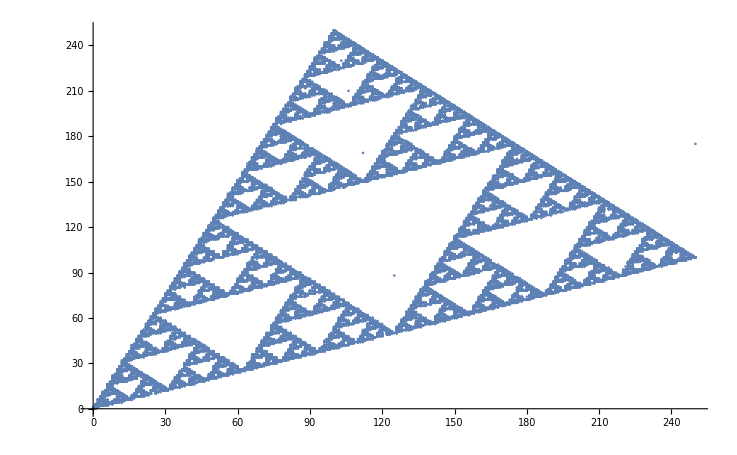

```mathematica
ListPlot[sierpinskiCarpet,PlotStyle->PointSize[0.0025]]
```

Note that the starting point quickly adjusts to the vertices, first finding its way into the central blank space, and then descending through the layers of recursive blanks until it gets to one small enough that it merges into the walls and starts tracing out the rest of the carpet. For the remainder of this notebook, I will call this merging process, “getting lost in the sauce.” At this particular resolution, the point appears to lose itself in sauce at the fifth layer of recursion.

You may also notice that the figure has stripes appearing vertically. These are the result of rounding the coordinate pairs to the nearest integer to lessen the computational load of generation. If we refer to them later, we will call this, “the stripey-wipey effect.”